```mathematica
f=2*Log[1+Cos[h]]
D[f,h]
```

2 Log[1+Cos[h]]

-(2 Sin[h])/(1+Cos[h])

```mathematica
Aphi=r*(1-Cos[h])+2*(1+Cos[h])*(1-Log[1+Cos[h]])
Aphi=r*(1-Cos[h])
(*Aphi=r^2*Sin[h]*)
gdetBr=FullSimplify[D[Aphi,h]]
```

r (1-Cos[h])+2 (1+Cos[h]) (1-Log[1+Cos[h]])

r (1-Cos[h])

r Sin[h]

```mathematica
mygdetBr=gdetBr//.{r->2}
myAphi=Aphi//.{r->2}
```

2 Sin[h]

2 (1-Cos[h])

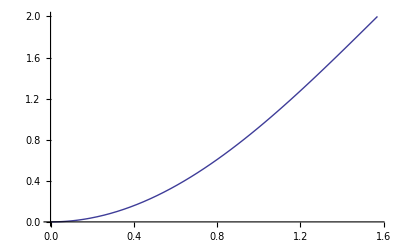

```mathematica
Plot[myAphi,{h,0,Pi/2}]
```